1. Сформулировать в системе Mathematica заданную формулу f(t).Продолжить её периодически на всю числовую прямую

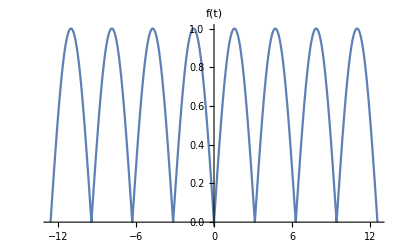

Рассчитать значения коэффициентов Фурье C_k, k = 1,2,...,N, разложения f(t) по тригонометрическому базису.

1.27324

0

-4/(3 π)

0 | 0
-4/(3 π) | 0
0 | 0
-4/(15 π) | 0
0 | 0
-4/(35 π) | 0
0 | 0
-4/(63 π) | 0
0 | 0
-4/(99 π) | 0

3. Cоставить программу апроксимации f(t) тригонометричким многочленам.Найти значение суммы ряда  любого t

Ряд при n = 2:

0.63662-(4 Cos[2 t])/(3 π)

Ряд при n = 3:

0.63662-(4 Cos[2 t])/(3 π)

Ряд при n = 5:

0.63662-(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)

Ряд при n = 8:

0.63662-(4 Cos[2 t])/(3 π)-(4 Cos[4 t])/(15 π)-(4 Cos[6 t])/(35 π)-(4 Cos[8 t])/(63 π)

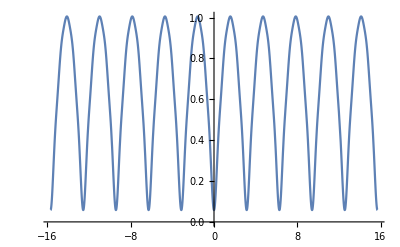

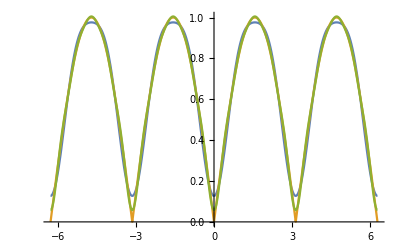

4. Проверить выполнение неравенства Парсеваля для заданного N=8,16.

NSum::nsumz: Some terms are zero. The algorithms are not very applicable.

0.999986

1.

0.999971

1.

0.999971

1.

5. Построить график функции f(t) и её апроксимации для заданного значения N=8,16. Провести анализ качеств разложения при различных N

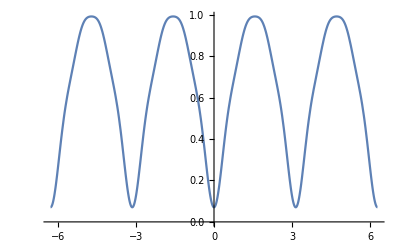

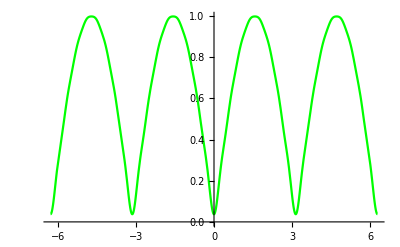

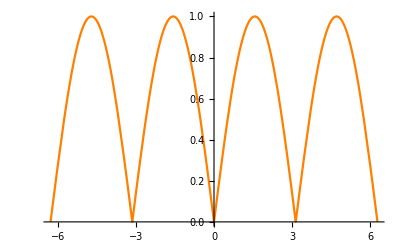

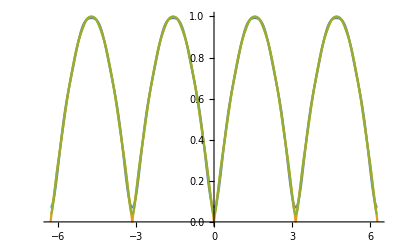

При увеличении N степень погрешность уменьшается.

6. Построить график ошибки ϵ_N(t)=f(t)-S_N(t).Расммотреть случай N=8,16.

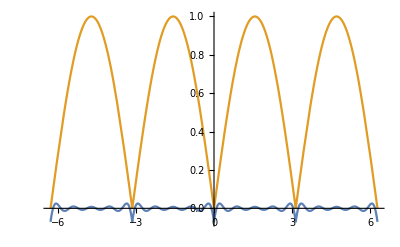

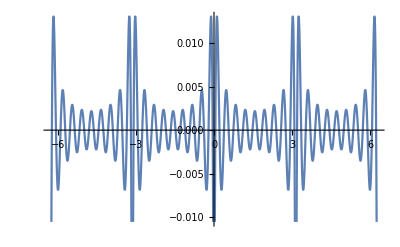

7. Рассчитать значения среднеквадратической ошибки для случая N=8,16

0.0306631

0.0166873

```mathematica
Clear[f]
Text["1. Сформулировать в системе Mathematica заданную формулу f(t).Продолжить её периодически на всю числовую прямую "]
f[t_]:=Abs[Sin[t]]/;-Pi≤t≤Pi
f[t_]:=f[t-2*Pi]/;t>Pi
f[t_]:=f[t+2*Pi]/;t<-Pi
Plot[f[t],{t,-4*Pi,4*Pi},PlotLabel->"f(t)"]
Text["Рассчитать значения коэффициентов Фурье C_k, k = 1,2,...,N, разложения f(t) по тригонометрическому базису."]
Clear[a,b,fs,L,ex,a1,b1]
L=Pi;
a[0]:=1/L*NIntegrate[f[t],{t,-L,L}];
a[0]
a[k_]:=1/L*NIntegrate[f[t]*Cos[k*t],{t,-L,L}];
b[k_]:=1/L*NIntegrate[f[t]*Sin[k*t],{t,-L,L}];
a1[k_]:=0/;Mod[k,2]≠0
a1[k_]:=-4/(Pi*(k^2-1))/;Mod[k,2]==0
b1[k_]:=0;
a1[1]
a1[2]
coeffs=Table[{a1[i],b1[i]},{i,1,10}];
TableForm[coeffs]
Text["Функция f(t) чётная, поэтому коэффициенты b_k = 0"];
Text["3. Cоставить программу апроксимации f(t) тригонометричким многочленам.Найти значение суммы ряда  любого t"]
Clear[row,rowSum,rowSeries]
row[n_,t_]:= a[0]/2+Sum[a1[k]*Cos[k*t],{k,1,n}];
Style[Text["Ряд при n = 2: "],"Italic"]
row[2,t]
Style[Text["Ряд при n = 3: "],"Italic"]
row[3,t]
Style[Text["Ряд при n = 5: "],"Italic"]
row[5,t]
Style[Text["Ряд при n = 8: "],"Italic"]
row[8,t]
graph10=Plot[row[10,t],{t,-5*Pi,5*Pi}]
graph410F=Plot[{row[4,t],f[t],row[10,t]},{t,-2*Pi,2*Pi}]
Text["4. Проверить выполнение неравенства Парсеваля для заданного N=8,16."]
Clear[parsevalLeft,parsevalRight]
parsevalLeft:=a[0]^2/2+∑_(n=1)^∞ (a1[n]^2+b1[n]^2);
parsevalRight:=1/Pi*NIntegrate[f[t]^2,{t,-Pi,Pi}]
N[parsevalLeft]
parsevalRight
parsevalLeft=a[0]^2/2+a1[2]^2+a1[4]^2+a1[6]^2+a1[8]^2+a1[10]^2+a1[12]^2+a1[14]^2+a1[16]^2+a[18]^2+a[20]^2
parsevalRight=1/Pi*NIntegrate[f[t]^2,{t,-Pi,Pi}]
parsevalLeft
parsevalRight
Text["5. Построить график функции f(t) и её апроксимации для заданного значения N=8,16. Провести анализ качеств разложения при различных N "]
Plot[row[8,t],{t,-2*Pi,2*Pi}]
Plot[row[16,t],{t,-2*Pi,2*Pi},PlotStyle->Green]
Plot[f[t],{t,-2*Pi,2*Pi},PlotStyle->Orange]
graph410F=Plot[{row[8,t],f[t],row[16,t]},{t,-2*Pi,2*Pi}]
Text["При увеличении N степень погрешность уменьшается."]
Text["6. Построить график ошибки ϵ_N(t)=f(t)-S_N(t).Расммотреть случай N=8,16. "]
Clear[eps8,eps16]
eps8[t_]:=f[t]-(a[0]/2+∑_(n=1)^8 (a1[n]*Cos[n*t]));
eps16[t_]:=f[t]-(a[0]/2+∑_(n=1)^16 (a1[n]*Cos[n*t]));
Plot[{eps8[t],f[t]},{t,-2*Pi,2*Pi}]
Plot[eps16[t],{t,-2*Pi,2*Pi}]
Text["7. Рассчитать значения среднеквадратической ошибки для случая N=8,16 "]
Clear[err8,err16]
err8=Sqrt[(eps8[-3]^2+eps8[-2]^2+eps8[-1]^2+eps8[0]^2+eps8[1]^2+eps8[2]^2+eps8[3]^2)/6];
err16 = Sqrt[(eps16[-3]^2+eps16[-2]^2+eps16[-1]^2+eps16[0]^2+eps16[1]^2+eps16[2]^2+eps16[3]^2)/6];
err8
err16
```